```mathematica
SetDirectory["C:\\Users\\Laura Sagunski\\Laura Dropbox (1)\\Laura Sagunski\\Self-interaction cross section\\Code\\Plots"]
```

C:\Users\Laura Sagunski\Laura Dropbox (1)\Laura Sagunski\Self-interaction cross section\Code\Plots

## Constants

```mathematica
(*hbar=1.;
c=2.995*10^5(*km/s*);*)
```

## Yukawa potential:

```mathematica
Uattractive[r_]=+hbar c αχ/r ⅇ^(-c/hbar mϕ r)
Urepulsive[r_]=-hbar c αχ/r ⅇ^(-c/hbar mϕ r)
```

(c ⅇ^(-(c mϕ r)/hbar) hbar αχ)/r

-(c ⅇ^(-(c mϕ r)/hbar) hbar αχ)/r

```mathematica
Normal[Series[Uattractive[r],{r,0,0}]]
```

-c^2 mϕ αχ+(c hbar αχ)/r

```mathematica
Normal[Series[Urepulsive[r],{r,0,0}]]
```

c^2 mϕ αχ-(c hbar αχ)/r

```mathematica
Solve[-αχ/r==(hbar^2 k^2)/(2 m)//.{m-> mχ/2,r-> r0,r0-> l/k,k-> p/hbar,(*k*)p-> a b mϕ,v-> 2 αχ a c, αχ-> b mϕ/mχ},l]
```

{{l→-1/(a hbar)}}

```mathematica
Normal[Series[BesselK[1,x],{x,0,1}]]
```

1/x+1/4 x (-1+2 EulerGamma-2 Log[2]+2 Log[x])

## Phase shift δl in classical regime

### Exact integral for δl

Landau, Lifshitz, p. 487, (126.4) :

```mathematica
integrandδlclass[l_,U_,r_]=1/hbar √(2m(EE-U)-(hbar^2(l+1/2)^2)/r^2)
```

(√(-(hbar^2 (1/2+l)^2)/r^2+2 m (EE-U)))/hbar

```mathematica
integrandδlclass2[l_,U_,r_]=k*c^2*(√(1-r0^2/r^2-U/(EE*c^2))-√(1-r0^2/r^2))
```

c^2 k (-√(1-r0^2/r^2)+√(1-r0^2/r^2-U/(c^2 EE)))

```mathematica
(*δlclassattractive[l_]:=NIntegrate[integrandδlclass[l,Uattractive[r],r],{r,r0,∞}](*//.{r0-> l/k}*)
δlclassrepulsive[l_]:=NIntegrate[integrandδlclass[l,Uattractive[r],r],{r,r0,∞}](*//.{r0-> l/k}*)*)
```

### Derivation of the approximate integral for δl

Landau, Lifshitz, ‘The quasi-classical case’, p. 487, (126.4) :

```mathematica
integrandδlclass[U]=1/hbar √(2m(EE-U)-(hbar^2(l+1/2)^2)/r^2)-k+1/2 π (l+1/2)-k r0
```

-k+1/2 (1/2+l) π-k r0+(√(-(hbar^2 (1/2+l)^2)/r^2+2 m (EE-U)))/hbar

```mathematica
Normal[Series[integrandδlclass[U],{U,0,1}]]
```

-k+π/4+(l π)/2+(√(2 EE m-(hbar^2 (1/2+l)^2)/r^2))/hbar-k r0-(m U)/(hbar √(2 EE m-(hbar^2 (1/2+l)^2)/r^2))

```mathematica
integrandδlclassappr1[r]=Part[Normal[Series[integrandδlclass[U],{U,0,1}]],{1,2}]
```

-k+π/4

```mathematica
integrandδlclassappr1[r]//.{2m EE-> hbar^2 k^2}//.{(l+1/2)^2-> l^2}//.{l-> k*r0}//.{√(hbar^2 k^2-(hbar^2 k^2 r0^2)/r^2)-> hbar k √(1-r0^2/r^2)}
```

-k+π/4

```mathematica
δlclassappr1[r]=Integrate[integrandδlclassappr1[r]//.{2m EE-> hbar^2 k^2}//.{(l+1/2)^2-> l^2}//.{l-> k*r0}//.{√(hbar^2 k^2-(hbar^2 k^2 r0^2)/r^2)-> hbar k √(1-r0^2/r^2)},{r,r0,∞},Assumptions-> {r0>0}](*Need all of these approximations.*)
```

(-k+π/4) ∞

```mathematica
δlclassappr2[r]=integrandδlclassappr2[r]=Part[Normal[Series[integrandδlclass[U],{U,0,1}]],3]
```

(l π)/2

```mathematica
δlclassappr=δlclassappr1[r]+δlclassappr2[r]+1/2 π(l+1/2)-k r0//.{2m EE-> hbar^2 k^2}//.{l+1/2-> l}//.{l-> k*r0}//.{(m U)/(hbar √(hbar^2 k^2-(hbar^2 k^2 r0^2)/r^2))-> (m U)/(hbar k √(1-r0^2/r^2))}//Expand
```

-k r0+k π r0+k (-∞)+∞

Landau, Lifshitz, p. 473, (123.1) :

```mathematica
integrandδlclassappr[U_,r_]=-(mχ/2)/hbar^2*U*1/(√(k^2-(l+1/2)^2/r^2))
```

-(mχ U)/(2 hbar^2 √(k^2-(1/2+l)^2/r^2))

### Approximate integral for δl

Landau, Lifshitz, p. 473, (123.1) :

```mathematica
integrandδlclassappr[U_,r_]:=-m/hbar^2*U*1/(√(k^2-(l+1/2)^2/r^2))
```

### Analytical solution of the integral for δl

Phase shift δl:

```mathematica
int2=(integrandδlclass[l,Uattractive[r],r])^2//.{EE-> (hbar^2 k^2)/(2 m)}//.{(l+1/2)^2-> l^2}//.{l-> k*r0,m-> mχ/2}//.{k-> (*(mχ v)/(2 hbar)*)c/hbar a b mϕ,(*,v-> 2 αχ a c,*)mχ->(mϕ b)/αχ(*,beta=1/(2 a^2 b)* b-> 2 a^2 beta*)}//.{mϕ-> (CC hbar)/(a b c)}//Expand
```

CC^2-(CC ⅇ^(-(CC r)/(a b)))/(a r)-(CC^2 r0^2)/r^2

```mathematica
Integrate[int2,{r,r0,∞}]
```

Integrate::idiv: Integral of 1-ⅇ^(-r/(a b))/(a r)-r0^2/r^2 does not converge on {r0,∞}.

∫_r0^∞ (1-ⅇ^(-r/(a b))/(a r)-r0^2/r^2)ⅆr

```mathematica
integrandδlclassappr[Uattractive[r],r]//.{(l+1/2)^2-> l^2}//.{l-> k*r0,m-> mχ/2}
```

-(c ⅇ^(-(c mϕ r)/hbar) mχ αχ)/(2 hbar r √(k^2-(k^2 r0^2)/r^2))

```mathematica
δlclassapprattractive[l_]=Integrate[integrandδlclassappr[Uattractive[r],r]//.{(l+1/2)^2-> l^2}//.{l-> k*r0,m-> mχ/2},{r,r0,∞},Assumptions-> {αχ >0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,c>0}]//.{r0-> l/k}
```

-(c mχ αχ BesselK[0,(c l mϕ)/(hbar k)])/(2 hbar k)

```mathematica
δlclassapprrepulsive[l_]=Integrate[integrandδlclassappr[Urepulsive[r],r]//.{(l+1/2)^2-> l^2}//.{l-> k*r0,m-> mχ/2},{r,r0,∞},Assumptions-> {αχ >0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,c>0}]//.{r0-> l/k}
```

(c mχ αχ BesselK[0,(c l mϕ)/(hbar k)])/(2 hbar k)

### Comparison of solutions for δl

```mathematica
m=mχ/2;
p=m v/c;
k=p/hbar;
EE=(hbar^2 k^2)/(2 m);
hbar= 1.;
αχ= 10.^-2;
mχ= 200.;
 mϕ= 10.^-3;
l=1.;
r0=l/k
v= 10.;
```

299.5

```mathematica
δlclassapprrepulsive[l]//.{k-> (mχ v)/(2 hbar),v-> 2 αχ a c,mχ->(mϕ b)/αχ}
```

BesselK[0,l/(a b)]/(2 a)

```mathematica
D[δlclassapprrepulsive[l]//.{k-> (mχ v)/(2 hbar),v-> 2 αχ a c,mχ->(mϕ b)/αχ},l]
```

-BesselK[1,l/(a b)]/(2 a^2 b)

```mathematica
Solve[Normal[Series[-BesselK[1,(*l/(a b)*)x]/(2 a^2 b),{x,0,0}]]==1//.{x->l/(a b) },l]
```

{{l→-1/(2 a)}}

```mathematica
Normal[Series[-BesselK[1,(*l/(a b)*)x]/(2 a^2 b),{x,0,4}]]==1//.{x->l/(a b) }
```

-1/(2 a l)+(l^3 (5-4 EulerGamma+4 Log[2]-4 Log[l/(a b)]))/(128 a^5 b^4)+(l (1-2 EulerGamma+2 Log[2]-2 Log[l/(a b)]))/(8 a^3 b^2)==1

```mathematica
Normal[Series[-BesselK[1,(*l/(a b)*)x]/(2 a^2 b),{x,∞,1}]]
```

-(ⅇ^-x √(π/2) √(1/x))/(2 a^2 b)

```mathematica
PadeApproximant[-BesselK[1,(*l/(a b)*)x]/(2 a^2 b),{x,∞,{1,1}}]
```

PadeApproximant[-BesselK[1,x]/(2 a^2 b),{x,∞,{1,1}}]

```mathematica
Normal[Series[ⅇ^-x,{x,0,2}]]
```

1-x+x^2/2

```mathematica
Normal[Series[√(1/x),{x,0,2}]]
```

1/(√x)

```mathematica
sol6=Solve[Normal[Series[-BesselK[1,(*l/(a b)*)x]/(2 a^2 b),{x,∞,1}]]==1//.{(*ⅇ^-x->( 1-x)*)√(1/x)-> √(1/(lminappr[beta]/(a b)))(*ⅇ^-x->ⅇ^(-lminappr[beta]/(a b))*)}//.{x->l/(a b) },l]//.{(*beta=1/(2 a^2 b)*)b-> 1/(2 a^2 beta)}
```

{{l→ConditionalExpression[(2 ⅈ π C[1]+Log[-(√((1/beta)^(3/2)/a) beta √π)/2^(3/4)])/(2 a beta),C[1]∈Integers]}}

```mathematica
Normal[Series[√(1/x),{x,∞,1}]]
```

√(1/x)

```mathematica
Solve[Normal[Series[-BesselK[1,(*l/(a b)*)x]/(2 a^2 b),{x,∞,1}]]==1//.{x->l/(a b) },l]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-(ⅇ^(-l/(a b)) √((a b)/l) √(π/2))/(2 a^2 b)==1,l]

```mathematica
Normal[Series[-BesselK[1,(*l/(a b)*)x]/(2 a^2 b),{x,0,1}]]//.{(*beta=1/(2 a^2 b)*)b-> 1/(2 a^2 beta)}
```

-beta/x+1/4 beta x (1-2 EulerGamma+2 Log[2]-2 Log[x])

```mathematica
EulerGamma//N
```

0.577216

```mathematica
sol2=Solve[Normal[Series[-BesselK[1,(*l/(a b)*)x]/(2 a^2 b),{x,0,1}]]==1//.{x->l/(a b) }//.{Log[l/(a b)]-> 0},l]//.{(*beta=1/(2 a^2 b)*)b-> 1/(2 a^2 beta)}
```

{{l→(-2/(a beta^2)-√(4/(a^2 beta^4)+(4 (1-2 EulerGamma+2 Log[2]))/(a^2 beta^2)))/(2 (-1+2 EulerGamma-2 Log[2]))},{l→(-2/(a beta^2)+√(4/(a^2 beta^4)+(4 (1-2 EulerGamma+2 Log[2]))/(a^2 beta^2)))/(2 (-1+2 EulerGamma-2 Log[2]))}}

```mathematica
sol3=Solve[Normal[Series[-BesselK[1,(*l/(a b)*)x]/(2 a^2 b),{x,0,1}]]==1//.{x->l/(a b) }//.{Log[l/(a b)]-> l/(a b)},l]//.{(*beta=1/(2 a^2 b)*)b-> 1/(2 a^2 beta)};
```

```mathematica
sol4=Solve[Normal[Series[-BesselK[1,(*l/(a b)*)x]/(2 a^2 b),{x,0,4}]]==1//.{x->l/(a b) }//.{Log[l/(a b)]-> 0},l]//.{(*beta=1/(2 a^2 b)*)b-> 1/(2 a^2 beta)};
```

```mathematica
sol5=Solve[Normal[Series[-BesselK[1,(*l/(a b)*)x]/(2 a^2 b),{x,0,1}]]==1//.{x->l/(a b) }//.{Log[l/(a b)]-> Log[((*l*)lminappr[beta])/(a b)]},l]//.{(*beta=1/(2 a^2 b)*)b-> 1/(2 a^2 beta)};
```

```mathematica
lminappr2[beta_]=Abs[l/.sol2[[2]]//.{(*beta=1/(2 a^2 b)*)a-> √(1/(2 beta))}]
```

Abs[-2 √2 (1/beta)^(3/2)+√(8/beta^3+(8 (1-2 EulerGamma+2 Log[2]))/beta)]/(2 (1-2 EulerGamma+2 Log[2]))

```mathematica
(1-2 EulerGamma+2 Log[2])//N
```

1.23186

```mathematica
lminappr3[beta_]=Abs[l/.sol3[[2]]//.{(*beta=1/(2 a^2 b)*)a-> √(1/(2 beta))}];
```

```mathematica
lminappr4[beta_]=Abs[l/.sol4[[2]]//.{(*beta=1/(2 a^2 b)*)a-> √(1/(2 beta))}];
```

```mathematica
lminappr5[beta_]=Abs[l/.sol5[[2]]//.{(*beta=1/(2 a^2 b)*)a-> √(1/(2 beta))}];
```

```mathematica
lminappr6[beta_]=l/.sol6[[1]]//.{(*beta=1/(2 a^2 b)*)a-> √(1/(2 beta))}//.{C[1]-> 1}
```

(ⅇ^(-2 beta) π)/(2 √2 (1/beta)^(3/2))

```mathematica
lminappr[beta_]=1/(2a)//.{(*beta=1/(2 a^2 b)*)a-> √(1/(2 beta))}
```

1/(√2 √(1/beta))

```mathematica
lmin[beta_]:=NSolve[Abs[-BesselK[1,(*l/(a b)*)x]/(2 a^2 b)]==1//.{x->l/(a b) }//.{b-> 1,(*beta=1/(2 a^2 b)*)a-> √(1/(2 beta))},l]
```

```mathematica
lmin[beta_]:=Module[{sol,lmin},
sol=FindRoot[Abs[-BesselK[1,(*l/(a b)*)x]/(2 a^2 b)]==1//.{x->l/(a b) }//.{b-> 1,(*beta=1/(2 a^2 b)*)a-> √(1/(2 beta))},{l,0.1(*lminappr[beta]*)(*initial guess*)}];
lmin=l/.sol;
lmin]
```

```mathematica
lminlargebeta[beta_]:=Module[{sol,lmin},
sol=FindRoot[Abs[Normal[Series[-BesselK[1,(*l/(a b)*)x]/(2 a^2 b),{x,∞,1}]]]==1//.{x->l/(a b) }//.{b-> 1,(*beta=1/(2 a^2 b)*)a-> √(1/(2 beta))},{l,0.1(*lminappr[beta]*)(*initial guess*)}];
lmin=l/.sol;
lmin]
```

```mathematica
lmin[1.]
```

0.512006

```mathematica
lminlargebeta[1.]
```

0.379595

```mathematica
betalminapprvals=Table[{10^logbeta,lminappr[10^logbeta]},{logbeta,-3.,3.,0.1}]
```

{{0.001,0.0223607},{0.00125893,0.0250891},{0.00158489,0.0281504},{0.00199526,0.0315853},{0.00251189,0.0354393},{0.00316228,0.0397635},{0.00398107,0.0446154},{0.00501187,0.0500593},{0.00630957,0.0561675},{0.00794328,0.063021},{0.01,0.0707107},{0.0125893,0.0793387},{0.0158489,0.0890195},{0.0199526,0.0998815},{0.0251189,0.112069},{0.0316228,0.125743},{0.0398107,0.141086},{0.0501187,0.158301},{0.0630957,0.177617},{0.0794328,0.19929},{0.1,0.223607},{0.125893,0.250891},{0.158489,0.281504},{0.199526,0.315853},{0.251189,0.354393},{0.316228,0.397635},{0.398107,0.446154},{0.501187,0.500593},{0.630957,0.561675},{0.794328,0.63021},{1.,0.707107},{1.25893,0.793387},{1.58489,0.890195},{1.99526,0.998815},{2.51189,1.12069},{3.16228,1.25743},{3.98107,1.41086},{5.01187,1.58301},{6.30957,1.77617},{7.94328,1.9929},{10.,2.23607},{12.5893,2.50891},{15.8489,2.81504},{19.9526,3.15853},{25.1189,3.54393},{31.6228,3.97635},{39.8107,4.46154},{50.1187,5.00593},{63.0957,5.61675},{79.4328,6.3021},{100.,7.07107},{125.893,7.93387},{158.489,8.90195},{199.526,9.98815},{251.189,11.2069},{316.228,12.5743},{398.107,14.1086},{501.187,15.8301},{630.957,17.7617},{794.328,19.929},{1000.,22.3607}}

```mathematica
betalminappr2vals=Table[{10^logbeta,lminappr2[10^logbeta]},{logbeta,-3.,3.,0.1}]
```

{{0.001,0.0223607},{0.00125893,0.0250891},{0.00158489,0.0281504},{0.00199526,0.0315853},{0.00251189,0.0354392},{0.00316228,0.0397634},{0.00398107,0.0446152},{0.00501187,0.0500589},{0.00630957,0.0561668},{0.00794328,0.0630197},{0.01,0.0707085},{0.0125893,0.0793348},{0.0158489,0.0890126},{0.0199526,0.0998692},{0.0251189,0.112047},{0.0316228,0.125705},{0.0398107,0.141018},{0.0501187,0.158179},{0.0630957,0.1774},{0.0794328,0.198904},{0.1,0.222922},{0.125893,0.249678},{0.158489,0.27936},{0.199526,0.312073},{0.251189,0.347762},{0.316228,0.38609},{0.398107,0.426275},{0.501187,0.466905},{0.630957,0.505825},{0.794328,0.540225},{1.,0.567059},{1.25893,0.583749},{1.58489,0.588863},{1.99526,0.582426},{2.51189,0.565741},{3.16228,0.540893},{3.98107,0.510229},{5.01187,0.475965},{6.30957,0.439974},{7.94328,0.403718},{10.,0.368262},{12.5893,0.334333},{15.8489,0.302383},{19.9526,0.272665},{25.1189,0.245278},{31.6228,0.220222},{39.8107,0.197427},{50.1187,0.176777},{63.0957,0.158137},{79.4328,0.141354},{100.,0.126276},{125.893,0.112752},{158.489,0.100639},{199.526,0.0897992},{251.189,0.080108},{316.228,0.071449},{398.107,0.0637164},{501.187,0.0568137},{630.957,0.050654},{794.328,0.0451587},{1000.,0.0402571}}

```mathematica
betalminappr3vals=Table[{10^logbeta,lminappr3[10^logbeta]},{logbeta,-3.,3.,0.1}];
```

```mathematica
betalminappr4vals=Table[{10^logbeta,lminappr3[10^logbeta]},{logbeta,-3.,3.,0.1}];
```

```mathematica
betalminappr5vals=Table[{10^logbeta,lminappr3[10^logbeta]},{logbeta,-3.,3.,0.1}];
```

```mathematica
betalminappr6vals=Table[{10^logbeta,lminappr6[10^logbeta]},{logbeta,-3.,3.,0.1}]
```

{{0.001,0.0000350539},{0.00125893,0.0000494893},{0.00158489,0.0000698599},{0.00199526,0.0000985988},{0.00251189,0.000139131},{0.00316228,0.000196272},{0.00398107,0.000276788},{0.00501187,0.000390168},{0.00630957,0.000549698},{0.00794328,0.000773937},{0.01,0.00108873},{0.0125893,0.00152992},{0.0158489,0.00214703},{0.0199526,0.00300798},{0.0251189,0.0042052},{0.0316228,0.00586324},{0.0398107,0.00814753},{0.0501187,0.0112739},{0.0630957,0.0155167},{0.0794328,0.0212134},{0.1,0.0287572},{0.125893,0.0385706},{0.158489,0.0510438},{0.199526,0.06642},{0.251189,0.0846107},{0.316228,0.104938},{0.398107,0.125838},{0.501187,0.144637},{0.630957,0.157602},{0.794328,0.160568},{1.,0.15032},{1.25893,0.126507},{1.58489,0.0931074},{1.99526,0.0578818},{2.51189,0.0290943},{3.16228,0.0111914},{3.98107,0.0030739},{5.01187,0.00055252},{6.30957,0.0000582343},{7.94328,3.13442×10^-6},{10.,7.23961×10^-8},{12.5893,5.76392×10^-10},{15.8489,1.2006×10^-12},{19.9526,4.62356×10^-16},{25.1189,2.12636×10^-20},{31.6228,6.73612×10^-26},{39.8107,7.35284×10^-33},{50.1187,1.15621×10^-41},{63.0957,8.73668×10^-53},{79.4328,7.964×10^-67},{100.,1.53712×10^-84},{125.893,7.0264×10^-107},{158.489,4.82538×10^-135},{199.526,1.5464×10^-170},{251.189,2.92362×10^-215},{316.228,1.3294×10^-271},{398.107,1.4259691312306×10^-342},{501.187,5.88714794494794×10^-432},{630.957,1.59594834618291×10^-544},{794.328,2.82401212982202×10^-686},{1000.,9.04984357771618×10^-865}}

```mathematica
betalminvals=Table[{10^logbeta,lmin[10^logbeta]},{logbeta,-3,3.,0.1}]
```

{{0.001,-0.0223606},{0.00125893,-0.025089},{0.00158489,0.0281502},{0.00199526,0.0315849},{0.00251189,0.0354386},{0.00316228,-0.0397623},{0.00398107,0.0446133},{0.00501187,0.0500556},{0.00630957,0.0561611},{0.00794328,0.0630101},{0.01,0.0706922},{0.0125893,0.0793073},{0.0158489,0.0889663},{0.0199526,0.0997916},{0.0251189,0.111917},{0.0316228,0.125488},{0.0398107,0.140659},{0.0501187,0.157589},{0.0630957,0.176435},{0.0794328,0.197341},{0.1,0.220416},{0.125893,0.245712},{0.158489,0.273188},{0.199526,0.302666},{0.251189,0.333792},{0.316228,0.366005},{0.398107,0.398534},{0.501187,0.430431},{0.630957,0.460648},{0.794328,0.488147},{1.,0.512006},{1.25893,0.53151},{1.58489,0.546201},{1.99526,0.555884},{2.51189,0.560604},{3.16228,0.560598},{3.98107,0.556244},{5.01187,0.54801},{6.30957,0.536413},{7.94328,0.521982},{10.,0.505237},{12.5893,0.486666},{15.8489,0.466721},{19.9526,0.445805},{25.1189,0.424277},{31.6228,0.402446},{39.8107,0.380577},{50.1187,0.358891},{63.0957,0.337573},{79.4328,0.31677},{100.,0.296599},{125.893,0.277151},{158.489,0.258493},{199.526,0.24067},{251.189,0.223712},{316.228,0.207634},{398.107,0.192438},{501.187,0.178117},{630.957,0.164657},{794.328,0.152036},{1000.,0.140227}}

```mathematica
betalminlargebetavals=Table[{10^logbeta,lminlargebeta[10^logbeta]},{logbeta,-3,3.,0.1}]
```

{{0.001,-0.0000351242},{0.00125893,-0.0000496143},{0.00158489,0.0000700812},{0.00199526,-0.0000989943},{0.00251189,-0.000139834},{0.00316228,0.000197511},{0.00398107,0.000278987},{0.00501187,0.000394067},{0.00630957,-0.000556749},{0.00794328,-0.000786486},{0.01,0.00111037},{0.0125893,0.00156815},{0.0158489,0.00221443},{0.0199526,0.00312653},{0.0251189,0.00441312},{0.0316228,0.00622651},{0.0398107,0.00877916},{0.0501187,-0.012562},{0.0630957,-0.0178281},{0.0794328,-0.025374},{0.1,-0.0362826},{0.125893,0.0473134},{0.158489,0.0651263},{0.199526,0.0885188},{0.251189,0.118251},{0.316228,0.154487},{0.398107,0.196482},{0.501187,0.242504},{0.630957,0.290099},{0.794328,0.336594},{1.,0.379595},{1.25893,0.417305},{1.58489,0.448607},{1.99526,0.473012},{2.51189,0.490515},{3.16228,0.501456},{3.98107,0.506389},{5.01187,0.50599},{6.30957,0.500979},{7.94328,0.492075},{10.,0.479964},{12.5893,0.465281},{15.8489,0.448598},{19.9526,0.430424},{25.1189,0.411204},{31.6228,0.391317},{39.8107,0.371089},{50.1187,0.350792},{63.0957,0.330649},{79.4328,0.310843},{100.,0.291519},{125.893,0.272792},{158.489,0.254748},{199.526,0.23745},{251.189,0.22094},{316.228,0.205245},{398.107,0.190377},{501.187,0.176338},{630.957,0.16312},{794.328,0.150706},{1000.,0.139076}}

```mathematica
Normal[Series[√(1-CC beta^2),{beta,0,2}]]
```

1-(beta^2 CC)/2

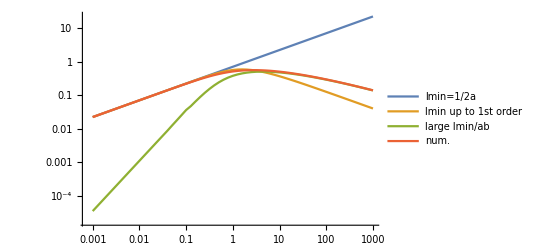

```mathematica
ListLogLogPlot[{betalminapprvals,betalminappr2vals,(*,betalminappr3vals,betalminappr4vals,betalminappr5vals,*)Abs[betalminlargebetavals],Abs[betalminvals]},Joined-> True,PlotRange-> All,PlotLegends->{"lmin=1/2a","lmin up to 1st order","large lmin/ab","num."}]
```

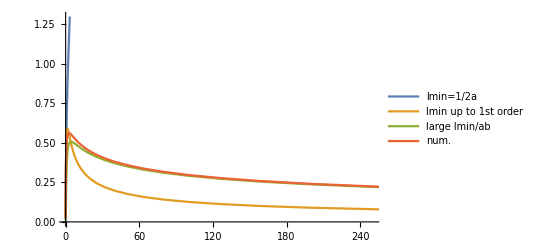

```mathematica
ListPlot[{betalminapprvals,betalminappr2vals,(*,betalminappr3vals,betalminappr4vals,betalminappr5vals,*)Abs[betalminlargebetavals],Abs[betalminvals]},Joined-> True,PlotRange-> Automatic,PlotLegends->{"lmin=1/2a","lmin up to 1st order","large lmin/ab","num."}]
```

```mathematica
data=Abs[betalminvals][[31;;]]
```

{{1.,0.512006},{1.25893,0.53151},{1.58489,0.546201},{1.99526,0.555884},{2.51189,0.560604},{3.16228,0.560598},{3.98107,0.556244},{5.01187,0.54801},{6.30957,0.536413},{7.94328,0.521982},{10.,0.505237},{12.5893,0.486666},{15.8489,0.466721},{19.9526,0.445805},{25.1189,0.424277},{31.6228,0.402446},{39.8107,0.380577},{50.1187,0.358891},{63.0957,0.337573},{79.4328,0.31677},{100.,0.296599},{125.893,0.277151},{158.489,0.258493},{199.526,0.24067},{251.189,0.223712},{316.228,0.207634},{398.107,0.192438},{501.187,0.178117},{630.957,0.164657},{794.328,0.152036},{1000.,0.140227}}

```mathematica
nlm=NonlinearModelFit[data,a ⅇ^(-b x^c),{a,b,c},x]
```

FittedModel[0.652969 ⅇ^(-0.125107 x^0.382147)]

FittedModel[0.908835 √(1/x)]

```mathematica
betalmintestvals=Table[{10^logbeta,nlm[10^logbeta]},{logbeta,-3,3.,0.1}]
```

{{0.001,0.590346},{0.00125893,0.59021},{0.00158489,0.590057},{0.00199526,0.589885},{0.00251189,0.589692},{0.00316228,0.589476},{0.00398107,0.589234},{0.00501187,0.588962},{0.00630957,0.588658},{0.00794328,0.588316},{0.01,0.587933},{0.0125893,0.587503},{0.0158489,0.587021},{0.0199526,0.586481},{0.0251189,0.585876},{0.0316228,0.585197},{0.0398107,0.584437},{0.0501187,0.583585},{0.0630957,0.582631},{0.0794328,0.581562},{0.1,0.580365},{0.125893,0.579024},{0.158489,0.577524},{0.199526,0.575846},{0.251189,0.573968},{0.316228,0.571869},{0.398107,0.569523},{0.501187,0.566901},{0.630957,0.563975},{0.794328,0.560709},{1.,0.557067},{1.25893,0.553009},{1.58489,0.548492},{1.99526,0.543466},{2.51189,0.537883},{3.16228,0.531686},{3.98107,0.524818},{5.01187,0.517218},{6.30957,0.508821},{7.94328,0.499562},{10.,0.489374},{12.5893,0.47819},{15.8489,0.465945},{19.9526,0.452578},{25.1189,0.438037},{31.6228,0.422277},{39.8107,0.405268},{50.1187,0.386997},{63.0957,0.367476},{79.4328,0.346743},{100.,0.32487},{125.893,0.301966},{158.489,0.278184},{199.526,0.253722},{251.189,0.228828},{316.228,0.203791},{398.107,0.178946},{501.187,0.154657},{630.957,0.131306},{794.328,0.109277},{1000.,0.0889285}}

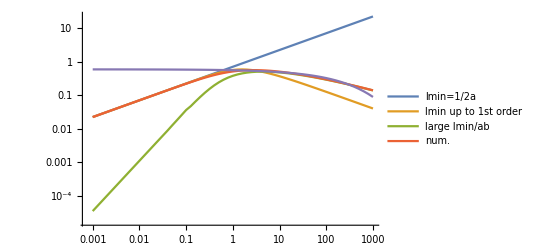

```mathematica
ListLogLogPlot[{betalminapprvals,betalminappr2vals,(*,betalminappr3vals,betalminappr4vals,betalminappr5vals,*)Abs[betalminlargebetavals],Abs[betalminvals],betalmintestvals},Joined-> True,PlotRange-> Automatic,PlotLegends->{"lmin=1/2a","lmin up to 1st order","large lmin/ab","num."}]
```

```mathematica
Export["ddelta_dl.pdf",%]
```

ddelta_dl.pdf

```mathematica
Plot[lmin[beta],{beta,10^-3,10^2}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

$Aborted

```mathematica
Normal[Series[-BesselK[1,(*l/(a b)*)x]/(2 a^2 b),{x,0,2}]]
```

-1/(2 a^2 b x)+(x (1-2 EulerGamma+2 Log[2]-2 Log[x]))/(8 a^2 b)

```mathematica
Normal[Series[-BesselK[1,(*l/(a b)*)x]/(2 a^2 b),{x,0,4}]](*//.{x->l/(a b) }*)(*//.{(*beta=1/(2 a^2 b)*)b->1/(2 a^2 beta)}*)
```

-1/(2 a^2 b x)+(x^3 (5-4 EulerGamma+4 Log[2]-4 Log[x]))/(128 a^2 b)+(x (1-2 EulerGamma+2 Log[2]-2 Log[x]))/(8 a^2 b)

```mathematica
Inuz[kmin_,kmax_,nu_,z_]=(1/2 z)^nu Sum[((1/4 z^2)^k)/(k! Gamma[nu+k+1]),{k,kmin,kmax}]
```

2^-nu z^nu (-(4^(-1-kmax) (z^2)^(1+kmax) HypergeometricPFQ[{1},{2+kmax,2+kmax+nu},z^2/4])/(Gamma[2+kmax] Gamma[2+kmax+nu])+(4^-kmin (z^2)^kmin HypergeometricPFQ[{1},{1+kmin,1+kmin+nu},z^2/4])/(Gamma[1+kmin] Gamma[1+kmin+nu]))

```mathematica
Inuz[0,1,1,x]//Expand
```

x/2+x^3/16

```mathematica
Normal[Series[BesselK[1,(*l/(a b)*)x],{x,0,2}]]
```

1/x+1/4 x (-1+2 EulerGamma-2 Log[2]+2 Log[x])

```mathematica
Solve[Normal[Series[-BesselK[1,(*l/(a b)*)x]/(2 a^2 b),{x,0,2}]]==1//.{Log[x]-> x-1}//.{x->l/(a b) },l]
```

{{l→1/6 (3 a b-2 a b EulerGamma+2 a b Log[2])+(48 a^4 b^3-(3 a b-2 a b EulerGamma+2 a b Log[2])^2)/(3 2^(2/3) (378 a^3 b^3+432 a^5 b^4+108 a^3 b^3 EulerGamma-288 a^5 b^4 EulerGamma-72 a^3 b^3 EulerGamma^2+16 a^3 b^3 EulerGamma^3-108 a^3 b^3 Log[2]+288 a^5 b^4 Log[2]+144 a^3 b^3 EulerGamma Log[2]-48 a^3 b^3 EulerGamma^2 Log[2]-72 a^3 b^3 Log[2]^2+48 a^3 b^3 EulerGamma Log[2]^2-16 a^3 b^3 Log[2]^3+√((378 a^3 b^3+432 a^5 b^4+108 a^3 b^3 EulerGamma-288 a^5 b^4 EulerGamma-72 a^3 b^3 EulerGamma^2+16 a^3 b^3 EulerGamma^3-108 a^3 b^3 Log[2]+288 a^5 b^4 Log[2]+144 a^3 b^3 EulerGamma Log[2]-48 a^3 b^3 EulerGamma^2 Log[2]-72 a^3 b^3 Log[2]^2+48 a^3 b^3 EulerGamma Log[2]^2-16 a^3 b^3 Log[2]^3)^2+4 (48 a^4 b^3-(3 a b-2 a b EulerGamma+2 a b Log[2])^2)^3))^(1/3))-1/(6 2^(1/3))(378 a^3 b^3+432 a^5 b^4+108 a^3 b^3 EulerGamma-288 a^5 b^4 EulerGamma-72 a^3 b^3 EulerGamma^2+16 a^3 b^3 EulerGamma^3-108 a^3 b^3 Log[2]+288 a^5 b^4 Log[2]+144 a^3 b^3 EulerGamma Log[2]-48 a^3 b^3 EulerGamma^2 Log[2]-72 a^3 b^3 Log[2]^2+48 a^3 b^3 EulerGamma Log[2]^2-16 a^3 b^3 Log[2]^3+√((378 a^3 b^3+432 a^5 b^4+108 a^3 b^3 EulerGamma-288 a^5 b^4 EulerGamma-72 a^3 b^3 EulerGamma^2+16 a^3 b^3 EulerGamma^3-108 a^3 b^3 Log[2]+288 a^5 b^4 Log[2]+144 a^3 b^3 EulerGamma Log[2]-48 a^3 b^3 EulerGamma^2 Log[2]-72 a^3 b^3 Log[2]^2+48 a^3 b^3 EulerGamma Log[2]^2-16 a^3 b^3 Log[2]^3)^2+4 (48 a^4 b^3-(3 a b-2 a b EulerGamma+2 a b Log[2])^2)^3))^(1/3)},{l→1/6 (3 a b-2 a b EulerGamma+2 a b Log[2])-((1+ⅈ √3) (48 a^4 b^3-(3 a b-2 a b EulerGamma+2 a b Log[2])^2))/(6 2^(2/3) (378 a^3 b^3+432 a^5 b^4+108 a^3 b^3 EulerGamma-288 a^5 b^4 EulerGamma-72 a^3 b^3 EulerGamma^2+16 a^3 b^3 EulerGamma^3-108 a^3 b^3 Log[2]+288 a^5 b^4 Log[2]+144 a^3 b^3 EulerGamma Log[2]-48 a^3 b^3 EulerGamma^2 Log[2]-72 a^3 b^3 Log[2]^2+48 a^3 b^3 EulerGamma Log[2]^2-16 a^3 b^3 Log[2]^3+√((378 a^3 b^3+432 a^5 b^4+108 a^3 b^3 EulerGamma-288 a^5 b^4 EulerGamma-72 a^3 b^3 EulerGamma^2+16 a^3 b^3 EulerGamma^3-108 a^3 b^3 Log[2]+288 a^5 b^4 Log[2]+144 a^3 b^3 EulerGamma Log[2]-48 a^3 b^3 EulerGamma^2 Log[2]-72 a^3 b^3 Log[2]^2+48 a^3 b^3 EulerGamma Log[2]^2-16 a^3 b^3 Log[2]^3)^2+4 (48 a^4 b^3-(3 a b-2 a b EulerGamma+2 a b Log[2])^2)^3))^(1/3))+1/(12 2^(1/3))(1-ⅈ √3) (378 a^3 b^3+432 a^5 b^4+108 a^3 b^3 EulerGamma-288 a^5 b^4 EulerGamma-72 a^3 b^3 EulerGamma^2+16 a^3 b^3 EulerGamma^3-108 a^3 b^3 Log[2]+288 a^5 b^4 Log[2]+144 a^3 b^3 EulerGamma Log[2]-48 a^3 b^3 EulerGamma^2 Log[2]-72 a^3 b^3 Log[2]^2+48 a^3 b^3 EulerGamma Log[2]^2-16 a^3 b^3 Log[2]^3+√((378 a^3 b^3+432 a^5 b^4+108 a^3 b^3 EulerGamma-288 a^5 b^4 EulerGamma-72 a^3 b^3 EulerGamma^2+16 a^3 b^3 EulerGamma^3-108 a^3 b^3 Log[2]+288 a^5 b^4 Log[2]+144 a^3 b^3 EulerGamma Log[2]-48 a^3 b^3 EulerGamma^2 Log[2]-72 a^3 b^3 Log[2]^2+48 a^3 b^3 EulerGamma Log[2]^2-16 a^3 b^3 Log[2]^3)^2+4 (48 a^4 b^3-(3 a b-2 a b EulerGamma+2 a b Log[2])^2)^3))^(1/3)},{l→1/6 (3 a b-2 a b EulerGamma+2 a b Log[2])-((1-ⅈ √3) (48 a^4 b^3-(3 a b-2 a b EulerGamma+2 a b Log[2])^2))/(6 2^(2/3) (378 a^3 b^3+432 a^5 b^4+108 a^3 b^3 EulerGamma-288 a^5 b^4 EulerGamma-72 a^3 b^3 EulerGamma^2+16 a^3 b^3 EulerGamma^3-108 a^3 b^3 Log[2]+288 a^5 b^4 Log[2]+144 a^3 b^3 EulerGamma Log[2]-48 a^3 b^3 EulerGamma^2 Log[2]-72 a^3 b^3 Log[2]^2+48 a^3 b^3 EulerGamma Log[2]^2-16 a^3 b^3 Log[2]^3+√((378 a^3 b^3+432 a^5 b^4+108 a^3 b^3 EulerGamma-288 a^5 b^4 EulerGamma-72 a^3 b^3 EulerGamma^2+16 a^3 b^3 EulerGamma^3-108 a^3 b^3 Log[2]+288 a^5 b^4 Log[2]+144 a^3 b^3 EulerGamma Log[2]-48 a^3 b^3 EulerGamma^2 Log[2]-72 a^3 b^3 Log[2]^2+48 a^3 b^3 EulerGamma Log[2]^2-16 a^3 b^3 Log[2]^3)^2+4 (48 a^4 b^3-(3 a b-2 a b EulerGamma+2 a b Log[2])^2)^3))^(1/3))+1/(12 2^(1/3))(1+ⅈ √3) (378 a^3 b^3+432 a^5 b^4+108 a^3 b^3 EulerGamma-288 a^5 b^4 EulerGamma-72 a^3 b^3 EulerGamma^2+16 a^3 b^3 EulerGamma^3-108 a^3 b^3 Log[2]+288 a^5 b^4 Log[2]+144 a^3 b^3 EulerGamma Log[2]-48 a^3 b^3 EulerGamma^2 Log[2]-72 a^3 b^3 Log[2]^2+48 a^3 b^3 EulerGamma Log[2]^2-16 a^3 b^3 Log[2]^3+√((378 a^3 b^3+432 a^5 b^4+108 a^3 b^3 EulerGamma-288 a^5 b^4 EulerGamma-72 a^3 b^3 EulerGamma^2+16 a^3 b^3 EulerGamma^3-108 a^3 b^3 Log[2]+288 a^5 b^4 Log[2]+144 a^3 b^3 EulerGamma Log[2]-48 a^3 b^3 EulerGamma^2 Log[2]-72 a^3 b^3 Log[2]^2+48 a^3 b^3 EulerGamma Log[2]^2-16 a^3 b^3 Log[2]^3)^2+4 (48 a^4 b^3-(3 a b-2 a b EulerGamma+2 a b Log[2])^2)^3))^(1/3)}}

```mathematica
Solve[Sin[x]^2==1//.{x-> -1/(2 a l)},l]
```

{{l→ConditionalExpression[1/(2 a (-π/2+2 π C[1])),C[1]∈Integers]},{l→ConditionalExpression[1/(2 a (π/2+2 π C[1])),C[1]∈Integers]},{l→ConditionalExpression[1/(2 a ((3 π)/2+2 π C[1])),C[1]∈Integers]}}

```mathematica
Normal[Series[-BesselK[1,(*l/(a b)*)x]/(2 a^2 b),{x,0,2}]]//.{x->l/(a b) }
```

-1/(2 a l)+(l (1-2 EulerGamma+2 Log[2]-2 Log[l/(a b)]))/(8 a^3 b^2)

```mathematica
Integrate[l BesselK[1,l]^2,l]
```

1/2 l^2 (BesselK[1,l]^2-BesselK[0,l] BesselK[2,l])

```mathematica
BesselK[0,0]
BesselK[0,∞]
```

∞

0

```mathematica
BesselK[1,0]
BesselK[1,∞]
```

ComplexInfinity

0

```mathematica
BesselK[2,∞]
BesselK[2,∞]
```

0

0

0

```mathematica
Integrate[l BesselK[1,l]^2,{l,1,∞},Assumptions-> {a>0,b>0}]
```

1/2 (BesselK[0,1]^2+2 BesselK[0,1] BesselK[1,1]-BesselK[1,1]^2)

```mathematica
Integrate[l BesselK[1,l/(a b)]^2,{l,1,∞},Assumptions-> {a>0,b>0}]
```

1/4 a^2 b^2 √π MeijerG[{{},{3/2}},{{0,0,2},{}},1/(a^2 b^2)]

```mathematica
Integrate[l Sin[BesselK[1,l/c]]^2,l,Assumptions-> {c>0}]
```

Integrate[l Sin[BesselK[1,l/c]]^2,l,Assumptions→{c>0}]

```mathematica
δlclassapprattractive[l]
```

-411.51

```mathematica
δlclassattractive=NIntegrate[integrandδlclass[l,Uattractive[r],r],{r,r0,(*∞*)100000.},PrecisionGoal->20,MinRecursion-> 10,MaxRecursion-> 15]-k+1/2 π (l+1/2)-k r0 (*Doesn't work well. Numerically very unstable.*)
```

135201.+57.4594 ⅈ

```mathematica
δlclassattractive2=NIntegrate[integrandδlclass2[l,Uattractive[r],r],{r,r0,(*∞*)10^2 r0},PrecisionGoal->20,MinRecursion-> 10,MaxRecursion-> 15]
```

-411.51+0.0104102 ⅈ

```mathematica
Normal[Series[Sin[x]^2,{x,0,4}]]
```

x^2-x^4/3

```mathematica
Integrate[l BesselK[1,l]^4,l]
```

∫l BesselK[1,l]^4ⅆl

## Transfer cross section σT

```mathematica
δlclassapprrepulsive[l]//.{k-> (mχ v)/(2 hbar),v-> 2 αχ a c,mχ->(mϕ b)/αχ}
```

BesselK[0,l/(a b)]/(2 a)

```mathematica
D[δlclassapprrepulsive[l]//.{k-> (mχ v)/(2 hbar),v-> 2 αχ a c,mχ->(mϕ b)/αχ},l]
```

-BesselK[1,l/(a b)]/(2 a^2 b)

### Integral (∫^∞)_lmin dl l (K_1(l/ab))^2

```mathematica
Integrate[l BesselK[1,l]^2,l]
```

1/2 l^2 (BesselK[1,l]^2-BesselK[0,l] BesselK[2,l])

```mathematica
Limit[Integrate[l BesselK[1,l]^2,l],l->0]
```

-∞

```mathematica
Limit[Integrate[l BesselK[1,l]^2,l],l->∞]
```

0

```mathematica
BesselK[0,0]
BesselK[0,∞]
```

∞

0

```mathematica
BesselK[1,0]
BesselK[1,∞]
```

ComplexInfinity

0

```mathematica
BesselK[0,∞]
BesselK[2,∞]
```

0

0

0

```mathematica
Integrate[l BesselK[1,l]^2,{l,0,∞}]
```

Integrate::idiv: Integral of l BesselK[1,l]^2 does not converge on {0,∞}.

∫_0^∞ l BesselK[1,l]^2ⅆl

```mathematica
Integrate[l BesselK[1,l]^2,{l,1,∞}]
```

1/2 (BesselK[0,1]^2+2 BesselK[0,1] BesselK[1,1]-BesselK[1,1]^2)

```mathematica
Integrate[l BesselK[1,l]^2,{l,1,∞}]-(BesselK[0,1] BesselK[2,1]-BesselK[1,1]^2)//Expand
```

1/2 BesselK[0,1]^2+BesselK[0,1] BesselK[1,1]+1/2 BesselK[1,1]^2-BesselK[0,1] BesselK[2,1]

```mathematica
Integrate[x BesselK[1,x]^2,x]
```

1/2 x^2 (BesselK[1,x]^2-BesselK[0,x] BesselK[2,x])

```mathematica
Integrate[x BesselK[1,x]^2,{x,1,∞}]
```

1/2 (BesselK[0,1]^2+2 BesselK[0,1] BesselK[1,1]-BesselK[1,1]^2)

```mathematica
Integrate[x BesselK[1,x]^2,{x,1/(a b),∞},Assumptions-> {a>0,b>0}]
```

1/4 √π MeijerG[{{},{3/2}},{{0,0,2},{}},1/(a^2 b^2)]

```mathematica
Integrate[l BesselK[1,l/(a b)]^2,{l,1,∞}]
```

ConditionalExpression[1/4 a^2 b^2 √π MeijerG[{{},{3/2}},{{0,0,2},{}},1/(a^2 b^2)],Re[1/(a b)]>0]

### Transfer cross section σT

```mathematica
(*from substitution*)(a*b)(*(l+1)*)l*(*sin^2(Subscript[δ, l+1]-Subscript[δ, l])*)(D[δlclassapprrepulsive[l]//.{k-> (mχ v)/(2 hbar),v-> 2 αχ a c,mχ->(mϕ b)/αχ},l])^2//.{l/(a b)-> x,(*beta=1/(2 a^2 b)*)b->1/(2 a^2 beta)}//.{l-> x a b}
```

1/2 b beta x BesselK[1,x]^2

```mathematica
indefiniteintegralσT[x_]=Integrate[(*from substitution*)(a*b)(*(l+1)*)l*(*sin^2(Subscript[δ, l+1]-Subscript[δ, l])*)(D[δlclassapprrepulsive[l]//.{k-> (mχ v)/(2 hbar),v-> 2 αχ a c,mχ->(mϕ b)/αχ},l])^2//.{l/(a b)-> x,(*beta=1/(2 a^2 b)*)b->1/(2 a^2 beta)}//.{l-> x a b},x]
```

1/4 b beta x^2 (BesselK[1,x]^2-BesselK[0,x] BesselK[2,x])

```mathematica
integralσT[a_,b_]=Limit[indefiniteintegralσT[x],x-> ∞]-indefiniteintegralσT[(*1/(a b)*)lmin/(a b)]//.{lmin-> 1/(2 a),(*beta=1/(2 a^2 b)*)b->1/(2 a^2 beta)}
```

-(beta^2 (BesselK[1,beta]^2-BesselK[0,beta] BesselK[2,beta]))/(8 a^2)

```mathematica
σTappr=(4π)/k^2*integralσT[a,b] //.{1/(a b)-> x,(*beta=1/(2 a^2 b)*)b->1/(2 a^2 beta)}//.{k-> (mχ v)/(2 hbar),v-> 2 αχ a c,mχ->(mϕ b)/αχ}(*//.{(*beta=1/(2 a^2 b)*)b->1/(2 a^2 beta)}*)
```

-(beta^2 hbar^2 π (BesselK[1,beta]^2-BesselK[0,beta] BesselK[2,beta]))/(2 a^4 b^2 c^2 mϕ^2)

```mathematica
σTappr=.
```

```mathematica
σTappr[beta_]=(4π)/k^2*integralσT[a,b] //.{1/(a b)-> x,(*beta=1/(2 a^2 b)*)b->1/(2 a^2 beta)}//.{k-> (mχ v)/(2 hbar),v-> 2 αχ a c,mχ->(mϕ b)/αχ}//.{(*beta=1/(2 a^2 b)*)b->1/(2 a^2 beta)}
```

-(2 beta^4 hbar^2 π (BesselK[1,beta]^2-BesselK[0,beta] BesselK[2,beta]))/(c^2 mϕ^2)

#### Comparison to phenomenological fit formula

Series expansion of σT for β<<1:

```mathematica
Normal[Series[σTappr[beta],{beta,0,2}]]
```

-(2 beta^2 π (1+2 EulerGamma-2 Log[2]+2 Log[beta]))/mϕ^2

```mathematica
Normal[Series[σTappr[beta],{beta,0,2}]]//.{1+2 EulerGamma-2 Log[2]-> 0}
```

-(4 beta^2 π Log[beta])/mϕ^2

```mathematica
σTphenosmallbeta[beta_]:=(4 π)/mϕ^2 beta^2 Log[1+1/beta]
```

```mathematica
Normal[Series[ σTphenosmallbeta[beta],{beta,0,2}]]
```

-(4 beta^2 π Log[beta])/mϕ^2

```mathematica
(*Ok.*)
```

Series expansion of σT for β>>1:

```mathematica
σTappr[beta]
```

-(2 beta^4 π (BesselK[1,beta]^2-BesselK[0,beta] BesselK[2,beta]))/mϕ^2

```mathematica
mϕ=1.
```

1.

1.

```mathematica
σTappr[x_]:=-6.283185307179586 (1/x)^4 (BesselK[1,(1/x)]^2-BesselK[0,(1/x)] BesselK[2,(1/x)])
```

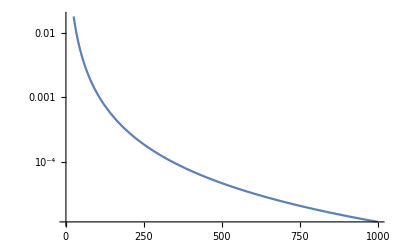

```mathematica
LogPlot[σTappr[x]/Log[x],{x,1,1000}]
```

```mathematica
Normal[Series[σTappr[1/x],{x,0,2}]]
```

ⅇ^(-2/x) (-(15 π^2)/(32 mϕ^2)+π^2/(mϕ^2 x^2)+(3 π^2)/(4 mϕ^2 x)+(75 π^2 x)/(128 mϕ^2)-(2205 π^2 x^2)/(2048 mϕ^2))

```mathematica
Normal[Series[σTappr[beta],{beta,∞,0}]]
```

ⅇ^(-2 beta) (-(15 π^2)/(32 mϕ^2)+(3 beta π^2)/(4 mϕ^2)+(beta^2 π^2)/mϕ^2)

```mathematica
Limit[σTappr[beta],beta-> ∞]
```

0

```mathematica
σTphenolargebeta[beta_]:=π/mϕ^2(Log[beta]+1-1/2(Log[beta])^-1)^2
```

```mathematica
Limit[σTphenolargebeta[beta],beta-> ∞,Assumptions-> {hbar>0,mϕ>0}]
```

∞

```mathematica
Normal[Series[ σTphenolargebeta[beta],{beta,∞,2}]]//.{Log[1/beta]-> Log[1]-Log[beta]}
```

(π-4 π Log[beta]+8 π Log[beta]^3+4 π Log[beta]^4)/(4 mϕ^2 Log[beta]^2)

#### Behavior of sigmaT for small/large velocities v

```mathematica
Normal[Series[σTappr[beta]//.{beta->(*1/(2 a^2 b)*)1/((*2 a b*)ϵ a)},{ϵ,∞,4}]]//.{ϵ-> a beta}//.{a->((*v/c*)v)/(2 αχ), beta-> (2 αχ mϕ)/(mχ (*(v/c)^2*)v^2)  }
```

-(32 mχ^4 π αχ^4 (-1+EulerGamma+Log[(mχ v)/mϕ]+Log[αχ/v]))/mϕ^6-(8 mχ^2 π αχ^2 (1+2 EulerGamma+2 Log[(mχ v)/mϕ]+2 Log[αχ/v]))/mϕ^4

```mathematica
σTapprvappr[v_]=Normal[Series[σTappr[beta]//.{beta->(*1/(2 a^2 b)*)1/((*2 a b*)ϵ a)},{ϵ,∞,2}]]//.{ϵ-> a beta}//.{a->((*v/c*)v)/(2 αχ), beta-> (2 αχ mϕ)/(mχ (*(v/c)^2*)v^2)  }
```

-(8 mχ^2 π αχ^2 (1+2 EulerGamma+2 Log[(mχ v)/mϕ]+2 Log[αχ/v]))/mϕ^4

```mathematica
Normal[Series[σTapprvappr[v],{v,0,0}]]
```

-(8 mχ^2 π αχ^2 (1+2 EulerGamma+2 Log[mχ/mϕ]+2 Log[αχ]))/mϕ^4

```mathematica
Normal[Series[σTapprvappr[v],{v,∞,4}]]
```

-(8 mχ^2 π αχ^2 (1+2 EulerGamma+2 Log[mχ/mϕ]+2 Log[αχ]))/mϕ^4

```mathematica
σTapprv[v_]=σTappr[beta]//.{beta-> (2 αχ mϕ)/(mχ (*(v/c)^2*)v^2)  }//.{mχ-> ϵ mϕ}
```

-(32 π αχ^4 (BesselK[1,(2 αχ)/(v^2 ϵ)]^2-BesselK[0,(2 αχ)/(v^2 ϵ)] BesselK[2,(2 αχ)/(v^2 ϵ)]))/(mϕ^2 v^8 ϵ^4)

Series expansion of σT for (v/c)<<1:

```mathematica
Normal[Series[σTapprv[v],{v,0,4}]]
```

ⅇ^(-(4 αχ)/(v^2 ϵ)) (-(15 π^2)/(32 mϕ^2)+(4 π^2 αχ^2)/(mϕ^2 v^4 ϵ^2)+(3 π^2 αχ)/(2 mϕ^2 v^2 ϵ)+(75 π^2 v^2 ϵ)/(256 mϕ^2 αχ)-(2205 π^2 v^4 ϵ^2)/(8192 mϕ^2 αχ^2))

```mathematica
Normal[Series[σTapprv[v],{ϵ,∞,2}]]
```

-(8 π αχ^2 (1+2 EulerGamma+2 Log[αχ/v^2]+2 Log[1/ϵ]))/(mϕ^2 v^4 ϵ^2)

```mathematica
Normal[Series[Normal[Series[σTapprv[v],{ϵ,∞,2}]],{v,0,4}]]
```

-(8 π αχ^2 (1+2 EulerGamma-4 Log[v]+2 Log[αχ]+2 Log[1/ϵ]))/(mϕ^2 v^4 ϵ^2)

Series expansion of σT for (v/c)>>1:

```mathematica
Normal[Series[σTapprv[v],{v,∞,4}]]//.{Log[1/v]->Log[1]-Log[v]}
```

-(8 π αχ^2 (1+2 EulerGamma-4 Log[v]+2 Log[αχ/ϵ]))/(mϕ^2 v^4 ϵ^2)

```mathematica
Normal[Series[Normal[Series[σTapprv[v],{ϵ,∞,2}]],{v,∞,4}]]//.{Log[1/v]->Log[1]-Log[v]}
```

-(8 π αχ^2 (1+2 EulerGamma-4 Log[v]+2 Log[αχ]+2 Log[1/ϵ]))/(mϕ^2 v^4 ϵ^2)

```mathematica
(*Proportional to 1/v^4. Ok.*)
```

```mathematica
D[δlclassapprrepulsive[l]//.{k-> (mχ v)/2,v-> 2 αχ a,mχ->(mϕ b)/αχ},l]
```

δlclassapprrepulsive'[l]

```mathematica
m=.;
k=.;
EE=.;
hbar=.;
αχ=.;
mχ=.;
 mϕ=.;
l=.;
r0=.
v=.;
```

```mathematica
δlclassapprattractive[l_]
```

-(mχ αχ BesselK[0,(mϕ l_)/k])/(2 hbar^2 k)

Sean’s formula, PRD87.115007, p.6, eqn. (9):

```mathematica
integrandσT[l_]=(l+1)*Sin[δlclassapprattractive[l+1]-δlclassapprattractive[l]]^2(*(δl[l+1]-δl[l])^2*)//FullSimplify//Expand
```

Sin[(mχ αχ (BesselK[0,(l mϕ)/k]-BesselK[0,((1+l) mϕ)/k]))/(2 hbar^2 k)]^2+l Sin[(mχ αχ (BesselK[0,(l mϕ)/k]-BesselK[0,((1+l) mϕ)/k]))/(2 hbar^2 k)]^2

```mathematica
integrandσTappr[l_]=(l+1)*(δlclassapprattractive[l+1]-δlclassapprattractive[l])^2(*(δl[l+1]-δl[l])^2*)
```

(1+l) ((mχ αχ BesselK[0,(l mϕ)/k])/(2 hbar^2 k)-(mχ αχ BesselK[0,((1+l) mϕ)/k])/(2 hbar^2 k))^2

```mathematica
σT=(4π)/k^2*Integrate[integrandσTappr[l],{l,(*lmin*)0,∞},Assumptions-> {αχ >0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0}]
```

(4 π Integrate[(1+l) ((mχ αχ BesselK[0,(l mϕ)/k])/(2 hbar^2 k)-(mχ αχ BesselK[0,((1+l) mϕ)/k])/(2 hbar^2 k))^2,{l,0,∞},Assumptions→{αχ>0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0}])/k^2

```mathematica
Normal[Series[integrandσTappr[l],{l,∞,0}]]
```

ⅇ^(-(2 l mϕ)/k) ((√(mϕ/k) mχ √(π/2) αχ)/(2 hbar^2 mϕ)-(ⅇ^(-mϕ/k) (k/mϕ)^(-1/2 Floor[Arg[mϕ/k]/(2 π)]) (mϕ/k)^(1/2-1/2 Floor[Arg[mϕ/k]/(2 π)]) mχ √(π/2) αχ)/(2 hbar^2 mϕ))^2

```mathematica
Integrate[Normal[Series[integrandσTappr[l],{l,∞,0}]],Assumptions-> {αχ >0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0}]
```

Integrate[ⅇ^(-(2 l mϕ)/k) ((√(mϕ/k) mχ √(π/2) αχ)/(2 hbar^2 mϕ)-(ⅇ^(-mϕ/k) (k/mϕ)^(-1/2 Floor[Arg[mϕ/k]/(2 π)]) (mϕ/k)^(1/2-1/2 Floor[Arg[mϕ/k]/(2 π)]) mχ √(π/2) αχ)/(2 hbar^2 mϕ))^2,Assumptions→{αχ>0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0}]

```mathematica
D[integrandσT[l],l]
```

(mχ αχ (-(mϕ BesselK[1,(l mϕ)/k])/k+(mϕ BesselK[1,((1+l) mϕ)/k])/k) Cos[(mχ αχ (BesselK[0,(l mϕ)/k]-BesselK[0,((1+l) mϕ)/k]))/(2 hbar^2 k)] Sin[(mχ αχ (BesselK[0,(l mϕ)/k]-BesselK[0,((1+l) mϕ)/k]))/(2 hbar^2 k)])/(hbar^2 k)+(l mχ αχ (-(mϕ BesselK[1,(l mϕ)/k])/k+(mϕ BesselK[1,((1+l) mϕ)/k])/k) Cos[(mχ αχ (BesselK[0,(l mϕ)/k]-BesselK[0,((1+l) mϕ)/k]))/(2 hbar^2 k)] Sin[(mχ αχ (BesselK[0,(l mϕ)/k]-BesselK[0,((1+l) mϕ)/k]))/(2 hbar^2 k)])/(hbar^2 k)+Sin[(mχ αχ (BesselK[0,(l mϕ)/k]-BesselK[0,((1+l) mϕ)/k]))/(2 hbar^2 k)]^2

```mathematica
Integrate[D[integrandσT[l],l],{l,(*lmin*)0,∞},Assumptions-> {αχ >0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0}]
```

Integrate[(mχ αχ (-(mϕ BesselK[1,(l mϕ)/k])/k+(mϕ BesselK[1,((1+l) mϕ)/k])/k) Cos[(mχ αχ (BesselK[0,(l mϕ)/k]-BesselK[0,((1+l) mϕ)/k]))/(2 hbar^2 k)] Sin[(mχ αχ (BesselK[0,(l mϕ)/k]-BesselK[0,((1+l) mϕ)/k]))/(2 hbar^2 k)])/(hbar^2 k)+(l mχ αχ (-(mϕ BesselK[1,(l mϕ)/k])/k+(mϕ BesselK[1,((1+l) mϕ)/k])/k) Cos[(mχ αχ (BesselK[0,(l mϕ)/k]-BesselK[0,((1+l) mϕ)/k]))/(2 hbar^2 k)] Sin[(mχ αχ (BesselK[0,(l mϕ)/k]-BesselK[0,((1+l) mϕ)/k]))/(2 hbar^2 k)])/(hbar^2 k)+Sin[(mχ αχ (BesselK[0,(l mϕ)/k]-BesselK[0,((1+l) mϕ)/k]))/(2 hbar^2 k)]^2,{l,0,∞},Assumptions→{αχ>0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0}]

```mathematica
σT=(4π)/k^2*Integrate[integrandσT[l],{l,(*lmin*)0,∞},Assumptions-> {αχ >0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0}] (*Integration with lmin as lower limit doesn't work.*)
```

1/k^2 4 π Integrate[Sin[(mχ αχ (BesselK[0,(l mϕ)/k]-BesselK[0,((1+l) mϕ)/k]))/(2 hbar^2 k)]^2+l Sin[(mχ αχ (BesselK[0,(l mϕ)/k]-BesselK[0,((1+l) mϕ)/k]))/(2 hbar^2 k)]^2,{l,0,∞},Assumptions→{αχ>0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0}]

```mathematica
Normal[Series[BesselK[0,(mϕ l)/k],{l,∞,0}]]
```

(ⅇ^(-(l mϕ)/k) k √(1/l) √(mϕ/k) √(π/2))/mϕ

```mathematica
BesselKappr[l_]=Normal[Series[BesselK[0,(mϕ l)/k],{l,∞,0}]]
```

(ⅇ^(-(l mϕ)/k) k √(1/l) √(mϕ/k) √(π/2))/mϕ

```mathematica
BesselKappr[l+1]-BesselKappr[l]//.{√(1/(1+l)) -> √(1/1) }//Simplify
```

(ⅇ^(-((1+l) mϕ)/k) (1-ⅇ^(mϕ/k) √(1/l)) √(π/2))/(√(mϕ/k))

```mathematica
Integrate[(l+1)*Sin[-(mχ αχ)/(2 hbar^2 k)(BesselKappr[l+1]-BesselKappr[l])//.{√(1/(1+l)) -> √(1/1) }//Simplify]^2,{l,(*lmin*)0,∞},Assumptions-> {αχ >0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0}]
```

Integrate[(1+l) Sin[(ⅇ^(-((1+l) mϕ)/k) (-1+ⅇ^(mϕ/k) √(1/l)) √(mϕ/k) mχ √(π/2) αχ)/(2 hbar^2 mϕ)]^2,{l,0,∞},Assumptions→{αχ>0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0}]

```mathematica
Normal[Series[integrandσT[l],{l,∞,0}]]
```

Sin[ⅇ^(-(l mϕ)/k) √(1/l) ((√(mϕ/k) mχ √(π/2) αχ)/(2 hbar^2 mϕ)-(ⅇ^(-mϕ/k) (k/mϕ)^(-1/2 Floor[Arg[mϕ/k]/(2 π)]) (mϕ/k)^(1/2-1/2 Floor[Arg[mϕ/k]/(2 π)]) mχ √(π/2) αχ)/(2 hbar^2 mϕ))]^2+l Sin[ⅇ^(-(l mϕ)/k) √(1/l) ((√(mϕ/k) mχ √(π/2) αχ)/(2 hbar^2 mϕ)-(ⅇ^(-mϕ/k) (k/mϕ)^(-1/2 Floor[Arg[mϕ/k]/(2 π)]) (mϕ/k)^(1/2-1/2 Floor[Arg[mϕ/k]/(2 π)]) mχ √(π/2) αχ)/(2 hbar^2 mϕ))]^2

```mathematica
Integrate[Normal[Series[integrandσT[l],{l,∞,0}]],{l,(*lmin*)0,∞},Assumptions-> {αχ >0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0}]
```

$Aborted

```mathematica
integrandσTappr[l_]=(l+1)*Sin[δlappr[l+1]-δlappr[l]]^2(*(δl[l+1]-δl[l])^2*)//FullSimplify//Expand
```

Sin[(ⅇ^(-((1+l) mϕ)/k) (-√l+ⅇ^(mϕ/k) √(1+l)) mχ √(π/2) αχ)/(2 hbar^2 √k √l √(1+l) √mϕ)]^2+l Sin[(ⅇ^(-((1+l) mϕ)/k) (-√l+ⅇ^(mϕ/k) √(1+l)) mχ √(π/2) αχ)/(2 hbar^2 √k √l √(1+l) √mϕ)]^2

```mathematica
σTappr=(4π)/k^2*Integrate[integrandσTappr[l],{l,(*lmin*)0,∞},Assumptions-> {αχ >0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0}]
```

$Aborted

```mathematica
integrandσTN[l_]=(l+1)*Sin[δl[l+1]-δl[l]]^2(*(δl[l+1]-δl[l])^2*)//.{k->mχ v/2,mχ-> 200, mϕ-> 0.00003,v-> 10/(2.99*10^5),αχ-> 1.6*10^-6,hbar-> 1}
```

(1+l) Sin[0.04784 BesselK[0,0.00897 l]-0.04784 BesselK[0,0.00897 (1+l)]]^2

```mathematica
σT=(4π)/k^2*NIntegrate[integrandσTN[l],{l,(*lmin*)0,(*∞*)10^5}]//.{k->mχ v/2,mχ-> 200, mϕ-> 0.00003,v-> 10/(2.99*10^5),αχ-> 1.6*10^-6,hbar-> 1}
```

19137.3

```mathematica
21419/19137.27625830608
```

1.11923

```mathematica
integrandσTN[l_]=(l+1)*Sin[δl[l+1]-δl[l]]^2(*(δl[l+1]-δl[l])^2*)//.{k->mχ v/2,mχ-> 1000, mϕ-> 0.001,v-> 100/(2.99*10^5),αχ-> 0.001,hbar-> 1}
```

(1+l) Sin[2.99 BesselK[0,0.00598 l]-2.99 BesselK[0,0.00598 (1+l)]]^2

```mathematica
σT=(4π)/k^2*NIntegrate[integrandσTN[l],{l,(*lmin*)0,(*∞*)(*10^5*)500}]//.{k->mχ v/2,mχ-> 1000, mϕ-> 0.001,v-> 100/(2.99*10^5),αχ-> 0.001,hbar-> 1}
```

16509.7

```mathematica
16519.358425530132/15429
```

1.07067

```mathematica
16519.358425530132/16333
```

1.01141

```mathematica
σTplot[lmax_]:=(4π)/k^2*NIntegrate[integrandσTN[l],{l,(*lmin*)0,(*∞*)(*10^5*)lmax}]//.{k->mχ v/2,mχ-> 1000, mϕ-> 0.001,v-> 100/(2.99*10^5),αχ-> 0.001,hbar-> 1}
```

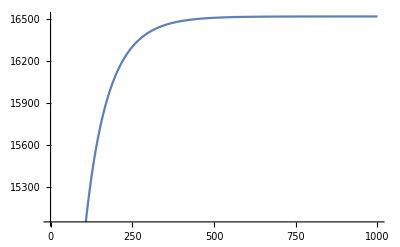

```mathematica
Plot[σTplot[lmax],{lmax,0,1000}]
```

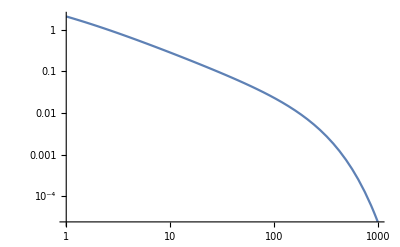

```mathematica
LogLogPlot[Abs[δl[l+1]-δl[l]//.{k->mχ v/2,mχ-> 1000, mϕ-> 0.001,v-> 100/(2.99*10^5),αχ-> 0.001,hbar-> 1}],{l,1,1000}]
```

```mathematica
integrandσT1[l_]=l*Sin[δl[l+1]-δl[l]]^2//.{(mχ αχ)/(hbar^2 k)-> c}
integrandσT2[l_]=Sin[δl[l+1]-δl[l]]^2//.{(mχ αχ)/(hbar^2 k)-> c}
```

l Sin[c BesselK[0,(l mϕ)/k]-c BesselK[0,((1+l) mϕ)/k]]^2

Sin[c BesselK[0,(l mϕ)/k]-c BesselK[0,((1+l) mϕ)/k]]^2

```mathematica
Integrate[integrandσT[l],{l,(*lmin*)0,∞},Assumptions-> {αχ >0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0,c>0}]
```

Integrate[(1+l) Sin[(mχ αχ (BesselK[0,(l mϕ)/k]-BesselK[0,((1+l) mϕ)/k]))/(hbar^2 k)]^2,{l,0,∞},Assumptions→{αχ>0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0,c>0}]

Formula Buckley, Fox, 0911.3898, p.2, eqn. (7):

```mathematica
integrandσT1Buckley[l_]=(2l+1)*Sin[δl[l]]^2//.{(mχ αχ)/(hbar^2 k)-> c}//FullSimplify
integrandσT2Buckley[l_]=-(2l+1)*Sin[δl[l]]*Sin[δl[l+1]]*Cos[δl[l+1]-δl[l]]//.{(mχ αχ)/(hbar^2 k)-> c}//FullSimplify
```

(1+2 l) Sin[c BesselK[0,(l mϕ)/k]]^2

-(1+2 l) Cos[c (BesselK[0,(l mϕ)/k]-BesselK[0,((1+l) mϕ)/k])] Sin[c BesselK[0,(l mϕ)/k]] Sin[c BesselK[0,((1+l) mϕ)/k]]

```mathematica
Integrate[integrandσT1Buckley[l],{l,(*lmin*)0,∞},Assumptions-> {αχ >0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0,c>0}]
```

Integrate[(1+2 l) Sin[c BesselK[0,(l mϕ)/k]]^2,{l,0,∞},Assumptions→{αχ>0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0,c>0}]

```mathematica
Integrate[integrandσT2Buckley[l],{l,(*lmin*)0,∞},Assumptions-> {αχ >0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0}]
```

Integrate[-(1+2 l) Cos[c (BesselK[0,(l mϕ)/k]-BesselK[0,((1+l) mϕ)/k])] Sin[c BesselK[0,(l mϕ)/k]] Sin[c BesselK[0,((1+l) mϕ)/k]],{l,0,∞},Assumptions→{αχ>0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0}]

## Differential cross section dσ/dΩ

See Buckley, Fox, 0911.3898, p.2, eqn. (5):

```mathematica
integranddσdΩ[l_]=(2l+1)*ⅇ^(ⅈ*δl[l])*LegendreP[l,Cos[θ]]* Sin[δl[l]]//FullSimplify
```

-1/2 ⅈ (-1+ⅇ^((2 ⅈ mχ αχ BesselK[0,(l mϕ)/k])/(hbar^2 k))) (1+2 l) LegendreP[l,Cos[θ]]

```mathematica
Integrate[integranddσdΩ[l],{l,(*lmin*)0,∞},Assumptions-> {αχ >0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0}]
```

Integrate[-1/2 ⅈ (-1+ⅇ^((2 ⅈ mχ αχ BesselK[0,(l mϕ)/k])/(hbar^2 k))) (1+2 l) LegendreP[l,Cos[θ]],{l,0,∞},Assumptions→{αχ>0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0}]